# NarvAC

### Autor: Carlos Manuel Rodríguez Martínez Email: fis.carlosmanuel@gmail.com

El objetivo de este proyecto es crear una máquina capaz de realizar cómputo a partir de compuertas lógicas.

-Graphics-

## Auxiliar

Ejecución

Definiciones necesarias para imitar el comportamiento de ciertos circuitos. MemoryEvaluate funciona creando un símbolo especial por cada tag, permitiendo así evaluar la función con el argumento de la evaluación anterior. Esto realiza una anidación de la función definida en expr por cada evaluación sucesiva.

```mathematica
HalfSplit[l_]:=TakeDrop[l, Floor[Length[l]/2]];

SetAttributes[MemoryEvaluate,HoldAll];
MemoryEvaluate[expr_,tag_]:=Block[{},
If[Head[MemorySymbol[tag]]== MemorySymbol,
MemorySymbol[tag] = 0;
];
MemorySymbol[tag] = ReleaseHold[expr[MemorySymbol[tag]]];
Return[MemorySymbol[tag]];
];

Unprotect[BitAnd];
BitAnd[1,x_]:=x;
BitAnd[x_,1]:=x;
Protect[BitAnd];

Unprotect[BitNot];
BitNot[0] := 1;
BitNot[1] := 0;
Protect[BitAnd];

DecimalToBinary[n_,size_ :8]:=PadLeft[IntegerDigits[n,2],size];
BinaryToDecimal[l_]:=FromDigits[l,2];
```

### Ejemplo

Ejemplo de uso de MemoryEvaluate

```mathematica
MemoryEvaluate[f,"Example"]
```

f[0]

```mathematica
MemoryEvaluate[f,"Example"]
```

f[f[0]]

```mathematica
MemoryEvaluate[f,"Example"]
```

f[f[f[0]]]

Visualización

### Visualización de resultados de circuitos.

```mathematica
VisualizeAdder[module_,inputSize_,flagName_] := Block[{logicTable,labels,gridList},
logicTable =  Map[Join[#,Apply[module,#]]&,Tuples[{0,1},inputSize]];
labels = Join[Take[Map[ToUpperCase,Alphabet[]],inputSize],{flagName,"Result"}];
gridList = Join[{labels},logicTable];
Grid[gridList,Frame->All,Background->{None,{LightGreen}}]
];

VisualizeMultiplexer[mux_,inputSize_]:=Block[{logicTable,labels,gridList},
logicTable =  Map[Join[#,{mux[#,Take[Alphabet[],2^inputSize]]}]&,Tuples[{0,1},inputSize]];
labels = Join[Take[Map[ToUpperCase,Alphabet[]],inputSize],{"Selection"}];
gridList = Join[{labels},logicTable];
Grid[gridList,Frame->All,Background->{None,{LightGreen}}]
];
```

### Visualización de la estructura de árbol

#### Evaluar sólo el encabezado

```mathematica
EvalWithValues[expr_,values_]:=expr/.values;
EvaluateHead[expr_,values_]:=ReplaceRepeated[expr,{f_Symbol[arg__]:>EvalWithValues[f[arg],values][arg]}];
```

```mathematica
DenestEvaluating[expr_,values_]:=
ReplaceAll[
Map[
If[Head[#]=== List,
DenestEvaluating[#,values],
EvaluateHead[#,values]
]&,
Level[expr,1]
],
values
];
```

#### Ejemplos (solo relevantes para la visualización)

```mathematica
expr = ALUAdder[{a1,a2},{b1,b2}]
```

{BitOr[BitAnd[b1,BitXor[a1,BitAnd[a2,b2]]],BitAnd[a1,a2,b2]],{BitXor[a1,b1,BitAnd[a2,b2]],BitXor[a2,b2]}}

```mathematica
DenestEvaluating[expr,{a1->0,a2->1,b1->0,b2->1}]
```

{0[0[0,1[0,1[1,1]]],0[0,1,1]],{1[0,0,1[1,1]],0[1,1]}}

#### Graficar expresión

```mathematica
SetOptions[$FrontEndSession,AutoStyleOptions->{"HighlightFormattingErrors"->False}];

SelectColor[coord_,edge_]:=
If[Head[First[edge]] =!=Symbol,
If[Last[edge]==1,
{ColorData["HTML"]["LawnGreen"],Line[coord]},
{GrayLevel[0.3],Line[coord]}
]
,
If[Head[Last[edge]] =!=Symbol,
If[Last[edge]==1,
{ColorData["HTML"]["LawnGreen"],Line[coord]},
{GrayLevel[0.3],Line[coord]}
]
,
{ColorData["HTML"]["SteelBlue"],Line[coord]}
]
];

PlotExpression[expr_,values_]:=Rasterize[
TreeForm[DenestEvaluating[expr,values],
VertexRenderingFunction->None,
EdgeRenderingFunction->(
ReleaseHold[SelectColor[#,#2]]&),
AspectRatio->1,
Background->Black
]
]
```

Forma alternativa, evaluar para cambiar de estilo

```mathematica
rules = Thread[{List,BitOr,BitAnd,BitXor,BitNot,0,1,Association}->RandomColor[8]]
```

```mathematica
rules = {List->RGBColor[0.9623193882679648, 0.03514590058516487, 0.5539986197144429],BitOr->RGBColor[0.4321980817159774, 0.2972881311143414, 0.8969615660840642],BitAnd->RGBColor[0.6169280698743795, 0.1544371325597096, 0.8820569584091065],BitXor->RGBColor[0.9874612892962218, 0.48338687273679914, 0.005451085259005284],BitNot->RGBColor[0.7522328767507627, 0.02288629260249042, 0.6068775359049052],0->RGBColor[0.8168930920991375, 0.6831040880488453, 0.015427844326858287],1->RGBColor[0.48095945766677284, 0.13406415167597507, 0.13390101182675873],Association->RGBColor[0.2947209985997292, 0.6655069057711502, 0.8296298604565884]};
GetColorForPlotExpression[f_,rules_]:=ReplaceAll[f,rules];
PlotExpression[expr_,values_]:=Block[{plt1,plt2,symbols,symbolRules},
plt1 = TreeForm[
DenestEvaluating[expr,values],
VertexRenderingFunction->None,
EdgeRenderingFunction->(
ReleaseHold[SelectColor[#,#2]]&),
AspectRatio->0.4,
Background->Black,
ImageSize->2200
];

symbols = GetSymbols[expr];
symbolRules = Join[rules,Thread[symbols->White]];
plt2 = TreeForm[
expr,
VertexRenderingFunction->({ReleaseHold[GetColorForPlotExpression[#2,symbolRules]],Disk[#,.05]}&),
EdgeRenderingFunction->None,
AspectRatio->0.4,
Background->Black,
ImageSize->2200
];

ImageAdd[Rasterize[plt1],0.4*Rasterize[plt2]]
];
```

#### Graficar sistema (sin necesidad de especificar el valor de las variables)

```mathematica
GetSymbols[system_]:=Complement[
DeleteDuplicates[Level[system,{-1},Heads->True]],
{List,BitOr,BitAnd,BitXor,BitNot,0,1,Association}
];

SetOptions[$FrontEndSession,DynamicEvaluationTimeout->20];
PlotInteractiveSystem[system_,plotVertex_:Automatic]:=DynamicModule[{symbols,controllerSymbols,boxes,controls,plot},
Clear["*Ctrl"];
symbols = GetSymbols[system];
controllerSymbols = Map[Symbol[StringJoin[SymbolName[#],"Ctrl"]]&,symbols];
boxes = Map[Checkbox[Dynamic[#],{0,1}]&,controllerSymbols];

controls = Panel[Multicolumn[Map[Row[{SymbolName[#[[1]]]<>": ",#[[2]]}]&,Transpose[{symbols,boxes}]],5],Style["Control",Bold]];

plot = Dynamic[
TreeForm[
DenestEvaluating[system,Thread[symbols->controllerSymbols]],
EdgeRenderingFunction->(
ReleaseHold[SelectColor[#,#2]]&),
VertexRenderingFunction->plotVertex,
ImageSize->400,
AspectRatio->1/2,
Background->Black
]
];

Column[{controls,Framed[plot]}]
];
```

## Multiplexor

2 a 1

-Graphics-

```mathematica
Mux2to1[{select_},{input1_,input2_}]:=BitOr[BitAnd[input1,BitNot[select]],BitAnd[input2,select]];
```

4 a 1

-Graphics-

```mathematica
Mux4to1[{select1_,select2_},{input1_,input2_,input3_,input4_}]:=Mux2to1[
{select1},
{
Mux2to1[{select2},{input1,input2}],
Mux2to1[{select2},{input3,input4}]
}
];
```

8 a 1

-Graphics-

```mathematica
Mux8to1[{select1_,select2_,select3_},{input1_,input2_,input3_,input4_,input5_,input6_,input7_,input8_}]:=
Mux2to1[
{select1},
{
Mux4to1[{select2,select3},{input1,input2,input3,input4}],
Mux4to1[{select2,select3},{input5,input6,input7,input8}]
}
];
```

Visualizaciones

Resultado

```mathematica
{VisualizeMultiplexer[Mux2to1,1],VisualizeMultiplexer[Mux4to1,2],VisualizeMultiplexer[Mux8to1,3]}
```

Árbol de complejidad

```mathematica
TreeForm[Mux8to1[{s1,s2,s3},{i1,i2,i3,i4,i5,i6,i7,i8}]]
```

Grid cuadrado

```mathematica
MultiplexerNTo1[2,{select_},input__]:=BitOr[BitAnd[First[input],BitNot[select]],BitAnd[Last[input],select]];
MultiplexerNTo1[n_,select_,input__]:=Block[{partInput},
partInput = HalfSplit[input];
MultiplexerNTo1[
2,
{First[select]},
{
MultiplexerNTo1[n/2,Rest[select],First[partInput]],
MultiplexerNTo1[n/2,Rest[select],Last[partInput]]
}
]
];
```

### Ejemplo

```mathematica
VisualizeMultiplexer[MultiplexerNTo1[16,#1,#2]&,4]
```

A | B | C | D | Selection
0 | 0 | 0 | 0 | a
0 | 0 | 0 | 1 | b
0 | 0 | 1 | 0 | c
0 | 0 | 1 | 1 | d
0 | 1 | 0 | 0 | e
0 | 1 | 0 | 1 | f
0 | 1 | 1 | 0 | g
0 | 1 | 1 | 1 | h
1 | 0 | 0 | 0 | i
1 | 0 | 0 | 1 | j
1 | 0 | 1 | 0 | k
1 | 0 | 1 | 1 | l
1 | 1 | 0 | 0 | m
1 | 1 | 0 | 1 | n
1 | 1 | 1 | 0 | o
1 | 1 | 1 | 1 | p

### Visualización

```mathematica
selectSymbols = Table[Symbol["s"<>ToString[i]],{i,1,8}];
inputSymbols = Table[Symbol["i"<>ToString[i]],{i,1,256}];
TreeForm[MultiplexerNTo1[256,selectSymbols,inputSymbols],VertexLabeling->Automatic,ImageSize->1300]
```

## Selección de Opcode por Multiplexor

Función auxiliar para ordenar los pares entrada-salida en los multiplexores

```mathematica
MuxInputByOpcode[n_,opcodeAndOutput_]:=Block[{addresses,missing},
addresses = Tuples[{0,1},n]; (* Generate the list of all opcode inputs.  *)
missing = Thread[{Complement[addresses,opcodeAndOutput[[All,1]]],0}]; (* Select the ones with no inputs and map them to zero. *)
Return[SortBy[Join[missing,opcodeAndOutput],First][[All,2]]] (* Join missing opcodes with the given opcodes and sort. *)
];

Multiplexer8Bit[opcode_,opcodeAndOutput_]:=Block[{opcodeLength = 8},
MultiplexerNTo1[2^opcodeLength,opcode,MuxInputByOpcode[opcodeLength,opcodeAndOutput]]
];

Multiplexer3Bit[opcode_,opcodeAndOutput_]:=Mux8to1[opcode,MuxInputByOpcode[3,opcodeAndOutput]];
```

### Ejemplo

```mathematica
MuxInputByOpcode[3,
{
{ALUOpCode["Add"],add},
{ALUOpCode["Substract"],substract},
{ALUOpCode["Decrement"],decrement}
}
]
```

{add,substract,0,decrement,0,0,0,0}

## ALU

Half adder

El Half Adder, Full Adder, y Ripple Carry Adder son circuitos para implementar sumas

-Graphics-

```mathematica
HalfAdder[a_,b_]:={BitAnd[a,b],BitXor[a,b]};
```

### Ejemplo

```mathematica
VisualizeAdder[HalfAdder,2,"Carry"]
```

A | B | Carry | Result
0 | 0 | 0 | 0
0 | 1 | 0 | 1
1 | 0 | 0 | 1
1 | 1 | 1 | 0

### Visualización

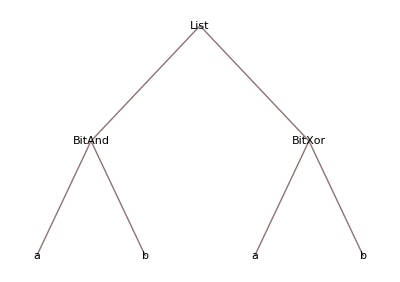

```mathematica
TreeForm[HalfAdder[a,b]]
```

```mathematica
HalfAdder[a,b]
```

{BitAnd[a,b],BitXor[a,b]}

Full adder

-Graphics-

```mathematica
FullAdder[a_,b_,c_]:=Block[{halfAdd1,halfAdd2},
halfAdd1 = HalfAdder[a,b];
halfAdd2 = HalfAdder[Last[halfAdd1],c];
{BitOr[First[halfAdd1],First[halfAdd2]],Last[halfAdd2]}
];
```

### Ejemplo

```mathematica
VisualizeAdder[FullAdder,3,"Carry"]
```

A | B | C | Carry | Result
0 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 1
0 | 1 | 0 | 0 | 1
0 | 1 | 1 | 1 | 0
1 | 0 | 0 | 0 | 1
1 | 0 | 1 | 1 | 0
1 | 1 | 0 | 1 | 0
1 | 1 | 1 | 1 | 1

### Visualización

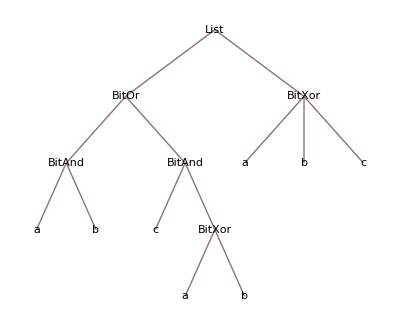

```mathematica
TreeForm[FullAdder[a,b,c]]
```

Ripple carry adder

-Graphics-

```mathematica
ALUAdder[A_,B_,carry_:0]:=Block[{littleEndianA,littleEndianB,pairs,sum,bigEndianSum},
littleEndianA = Reverse[A];
littleEndianB = Reverse[B];

(* Se crea conjunto de pares a sumar *)
pairs = Transpose[{littleEndianA,littleEndianB}];

(* Se añaden dos pares extra para la última adición *)
pairs = Join[pairs,{{0,0},{0,0}}];
sum = Drop[FoldPairList[{Last[#1],Apply[FullAdder,Join[{First[#1]},#2]]}&,{carry,0},pairs],1];
bigEndianSum = Reverse[sum];
Return[{First[bigEndianSum],Rest[bigEndianSum]}];
];
```

### Ejemplo

```mathematica
pairs = Tuples[{Tuples[{0,1},2],Tuples[{0,1},2]}];
result = MapThread[ALUAdder,Transpose[pairs]];
labels = {"A","B","Carry","Result"};
logicTable = MapThread[Join[#1,#2]&,{pairs,result}];
Grid[Join[{labels},logicTable],Frame->All,Background->{None,{LightGreen}}]
```

A | B | Carry | Result
{0,0} | {0,0} | 0 | {0,0}
{0,0} | {0,1} | 0 | {0,1}
{0,0} | {1,0} | 0 | {1,0}
{0,0} | {1,1} | 0 | {1,1}
{0,1} | {0,0} | 0 | {0,1}
{0,1} | {0,1} | 0 | {1,0}
{0,1} | {1,0} | 0 | {1,1}
{0,1} | {1,1} | 1 | {0,0}
{1,0} | {0,0} | 0 | {1,0}
{1,0} | {0,1} | 0 | {1,1}
{1,0} | {1,0} | 1 | {0,0}
{1,0} | {1,1} | 1 | {0,1}
{1,1} | {0,0} | 0 | {1,1}
{1,1} | {0,1} | 1 | {0,0}
{1,1} | {1,0} | 1 | {0,1}
{1,1} | {1,1} | 1 | {1,0}

### Visualización

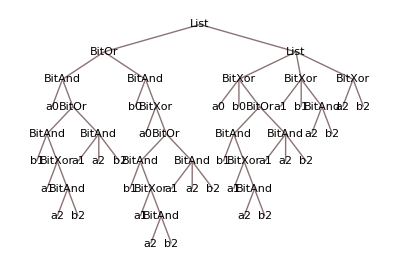

```mathematica
TreeForm[ALUAdder[{a0,a1,a2},{b0,b1,b2}]]
```

En esencia no deja de ser una composición de operaciones binarias

```mathematica
ALUAdder[{a0,a1,a2},{b0,b1,b2}]
```

{BitOr[BitAnd[a0,BitOr[BitAnd[b1,BitXor[a1,BitAnd[a2,b2]]],BitAnd[a1,a2,b2]]],BitAnd[b0,BitXor[a0,BitOr[BitAnd[b1,BitXor[a1,BitAnd[a2,b2]]],BitAnd[a1,a2,b2]]]]],{BitXor[a0,b0,BitOr[BitAnd[b1,BitXor[a1,BitAnd[a2,b2]]],BitAnd[a1,a2,b2]]],BitXor[a1,b1,BitAnd[a2,b2]],BitXor[a2,b2]}}

Substractor

```mathematica
ALUSubstractor[A_,B_,borrow_:1]:=Block[{littleEndianA,littleEndianB,pairs,sum,bigEndianSum},
littleEndianA = Reverse[A];
littleEndianB = Reverse[BitNot[B]];

(* Se crea conjunto de pares a sumar *)
pairs = Transpose[{littleEndianA,littleEndianB}];

(* Se añaden dos pares extra para la última adición *)
pairs = Join[pairs,{{0,0},{0,0}}];
sum = Drop[FoldPairList[{Last[#1],Apply[FullAdder,Join[{First[#1]},#2]]}&,{borrow,0},pairs],1];
bigEndianSum = Reverse[sum];
Return[{BitNot[First[bigEndianSum]],Rest[bigEndianSum]}];
];
```

### Ejemplo

```mathematica
pairs = Tuples[{Tuples[{0,1},2],Tuples[{0,1},2]}];
result = MapThread[ALUSubstractor,Transpose[pairs]];
labels = {"A","B","Borrow","Result"};
logicTable = MapThread[Join[#1,#2]&,{pairs,result}];
Grid[Join[{labels},logicTable],Frame->All,Background->{None,{LightGreen}}]
```

A | B | Borrow | Result
{0,0} | {0,0} | 0 | {0,0}
{0,0} | {0,1} | 1 | {1,1}
{0,0} | {1,0} | 1 | {1,0}
{0,0} | {1,1} | 1 | {0,1}
{0,1} | {0,0} | 0 | {0,1}
{0,1} | {0,1} | 0 | {0,0}
{0,1} | {1,0} | 1 | {1,1}
{0,1} | {1,1} | 1 | {1,0}
{1,0} | {0,0} | 0 | {1,0}
{1,0} | {0,1} | 0 | {0,1}
{1,0} | {1,0} | 0 | {0,0}
{1,0} | {1,1} | 1 | {1,1}
{1,1} | {0,0} | 0 | {1,1}
{1,1} | {0,1} | 0 | {1,0}
{1,1} | {1,0} | 0 | {0,1}
{1,1} | {1,1} | 0 | {0,0}

### Visualización

```mathematica
TreeForm[ALUSubstractor[{a0,a1,a2},{b0,b1,b2}]]
```

Opcodes

```mathematica
aluMnemonics = {"Add","Substract","Increment","Decrement","Pass"};
aluOpcodes = Thread[aluMnemonics->Take[Tuples[{0,1},3],Length[aluMnemonics]]];
revAluOpcodes = Map[Reverse,aluOpcodes];
ALUOpCode[mnemonic_]:=ReplaceAll[mnemonic,aluOpcodes];
```

```mathematica
Column@aluOpcodes
```

Add→{0,0,0}
Substract→{0,0,1}
Increment→{0,1,0}
Decrement→{0,1,1}
Pass→{1,0,0}

Ejecución

Banderas

```mathematica
ALUZero[a_]:=BitNot[Apply[BitOr,a]];
ALUNotZero[a_]:=Apply[BitOr,a];
ALUParity[a_]:=Apply[BitXor,a];
```

Ejecución

```mathematica
ALUExecute[opcode_,a_,b_]:=Block[
{
add,substract,
increment,decrement,pass,output,positiveFlag,
negativeFlag,parityFlag
},

add = ALUAdder[a,b];
substract = ALUSubstractor[a,b];
increment = ALUAdder[PadLeft[{1},Length[a]],a];
decrement = ALUSubstractor[a,PadLeft[{1},Length[a]]];
pass = a;

output = Multiplexer3Bit[opcode,
{
{ALUOpCode["Add"],Last[add]},
{ALUOpCode["Substract"],Last[substract]},
{ALUOpCode["Increment"],Last[increment]},
{ALUOpCode["Decrement"],Last[decrement]},
{ALUOpCode["Pass"],pass}
}
];

positiveFlag = Multiplexer3Bit[opcode,
{
{ALUOpCode["Add"],1},
{ALUOpCode["Substract"],BitNot[First[substract]]},
{ALUOpCode["Increment"],1},
{ALUOpCode["Decrement"],BitNot[First[decrement]]},
{ALUOpCode["Pass"],0}
}
];

negativeFlag = Multiplexer3Bit[opcode,
{
{ALUOpCode["Add"],0},
{ALUOpCode["Substract"],First[substract]},
{ALUOpCode["Increment"],0},
{ALUOpCode["Decrement"],First[decrement]},
{ALUOpCode["Pass"],0}
}
];

Return[<|"Positive"->positiveFlag,"Negative"->negativeFlag,"Zero"->ALUZero[output],"NotZero"->ALUNotZero[output],"Parity"->ALUParity[output],"Result"->output|>];
];
ALUExecute[opcode_,a_]:=ALUExecute[opcode,a,ConstantArray[0,Length[a]]];

ALUClear[]:=Block[{},
WriteFlag[0,"ALUFlagPositive"];
WriteFlag[0,"ALUFlagNegative"];
WriteFlag[0,"ALUFlagZero"];
WriteFlag[0,"ALUFlagNotZero"];
WriteFlag[0,"ALUFlagParity"];
];
```

### Visualización

```mathematica
BinaryToDecimal[ALUExecute[ALUOpCode["Add"],DecimalToBinary[11],DecimalToBinary[7]]["Result"]]
```

18

```mathematica
BinaryToDecimal[ALUExecute[ALUOpCode["Substract"],DecimalToBinary[11],DecimalToBinary[7]]["Result"]]
```

4

```mathematica
BinaryToDecimal[ALUExecute[ALUOpCode["Increment"],DecimalToBinary[11],DecimalToBinary[7]]["Result"]]
```

12

```mathematica
BinaryToDecimal[ALUExecute[ALUOpCode["Decrement"],DecimalToBinary[11],DecimalToBinary[7]]["Result"]]
```

10

```mathematica
ALUExecute[ALUOpCode["Pass"],DecimalToBinary[11],DecimalToBinary[7]]
```

<|Positive→0,Negative→0,Zero→0,NotZero→1,Parity→1,Result→{0,0,0,0,1,0,1,1}|>

Complejidad de una ALU de 2 bits

```mathematica
TreeForm[Normal[ALUExecute[{o1,o2,o3},{a1,a2},{b1,b2}]],PlotRangePadding->Scaled[.002]]
```

Complejidad de una ALU de 8 bits

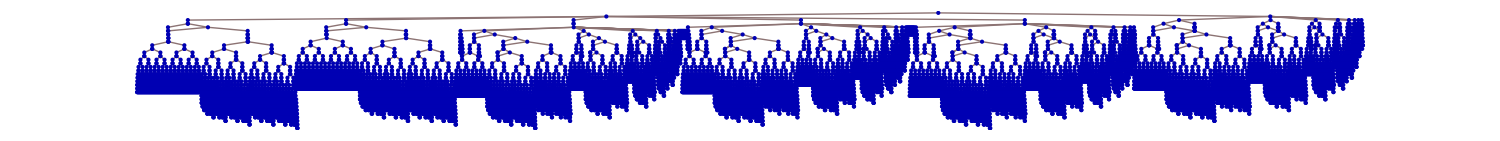

```mathematica
TreeForm[Normal[ALUExecute[{o1,o2,o3},{a1,a2,a3,a4,a5,a6,a7,a8},{b1,b2,b3,b4,b5,b6,b7,b8}]],VertexLabeling->Automatic,ImageSize->1500]
```

## Memoria

And-Or Latch

De la Wikipedia: In electronics, a flip-flop or latch is a circuit that has two stable states and can be used to store state information. A flip-flop is a bistable multivibrator. The circuit can be made to change state by signals applied to one or more control inputs and will have one or two outputs. It is the basic storage element in sequential logic. Flip-flops and latches are fundamental building blocks of digital electronics systems used in computers, communications, and many other types of systems.

-Graphics-

```mathematica
AndOrLatch[set_,reset_,tag_]:=MemoryEvaluate[BitAnd[BitOr[#,set],BitNot[reset]]&,tag];
```

Este es el circuito base para todos los tipos de memoria que se utiliza a continuación

### Visualización

```mathematica
Table[TreeForm[AndOrLatch[set,reset,tag],ImageSize->Medium],3]
```

Gated Latch

-Graphics-

Fuente: Crash Course Computer Science

```mathematica
GatedLatch[dataInput_,writeEnable_,tag_]:=AndOrLatch[BitAnd[dataInput,writeEnable],BitAnd[BitNot[dataInput],writeEnable],tag];
```

Estos circuitos nos sirven para guardar banderas de 1 bit

```mathematica
Flag[dataInput_,writeEnable_,tag_]:=GatedLatch[dataInput,writeEnable,tag];
ReadFlag[tag_]:=GatedLatch[0,0,tag];
WriteFlag[dataInput_,tag_]:=GatedLatch[dataInput,1,tag];
```

### Visualización

```mathematica
Table[TreeForm[GatedLatch[dataInput,writeEnable,tag],ImageSize->Medium,VertexRenderingFunction->None],3]
```

Celda

Fuente: Crash Course Computer Science

```mathematica
Bit8AddressCell[dataInput_,writeEnable_,address__,tag_]:=
GatedLatch[
dataInput,
writeEnable,
StringJoin[
tag,
"bit_",
ToString[
MultiplexerNTo1[
256,
address,
Range[256]
]
]
]
];
```

Bloque

Fuente: Crash Course Computer Science

```mathematica
Bit8AddressBlock[dataInput__/;Length[dataInput]==8,writeEnable_,address__,tag_]:=Table[Bit8AddressCell[Part[dataInput,i],writeEnable,address,StringJoin[tag,"bit_",ToString[i]]],{i,8}];

ReadBit8AddressBlock[address__,tag_]:=Bit8AddressBlock[{0,0,0,0,0,0,0,0},0,address,tag];
WriteBit8AddressBlock[dataInput__/;Length[dataInput]==8,address__,tag_]:=Bit8AddressBlock[dataInput,1,address,tag];

ResetBit8AddressBlock[tag_,size_]:=Block[{addresses},
addresses = Map[PadLeft[IntegerDigits[#,2],8]&,Range[0,size]];
Map[WriteBit8AddressBlock[{0,0,0,0,0,0,0,0},#1,tag]&,addresses];
];
```

### Visualización

```mathematica
TreeForm[Bit8AddressBlock[{b1,b2,b3,b4,b5,b6,b7,b8},writeEnable,{a1,a2,a3,a4,a5,a6,a7,a8},"exampletag"]]
```

```mathematica
TreeForm[Bit8AddressBlock[{b1,b2,b3,b4,b5,b6,b7,b8},writeEnable,{a1,a2,a3,a4,a5,a6,a7,a8},"exampletag"]]
```

Visualización recursiva interactiva

```mathematica
trees = Table[TreeForm[Bit8AddressBlock[{b1,b2,b3,b4,b5,b6,b7,b8},writeEnable,{a1,a2,a3,a4,a5,a6,a7,a8},"manip"],VertexLabeling->Automatic,ImageSize->1300],15];
Manipulate[trees[[i]],{i,1,Length[trees],1},SaveDefinitions->True]
```

## Registros

Fuente: Crash Course Computer Science

```mathematica
Bit3Register[dataInput__,writeEnable_,tag_]:=Table[
GatedLatch[
Part[dataInput,index],
writeEnable,
StringJoin[tag,"_bit3register",ToString[index]]
],
{index,1,3}
];
ReadBit3Register[tag_]:=Bit3Register[{0,0,0},0,tag];
WriteBit3Register[dataInput__,tag_]:=Bit3Register[dataInput,1,tag];

Bit8Register[dataInput__,writeEnable_,tag_]:=Table[
GatedLatch[
Part[dataInput,index],
writeEnable,
StringJoin[tag,"_bit8register",ToString[index]]
],
{index,1,8}
];
ReadBit8Register[tag_]:=Bit8Register[{0,0,0,0,0,0,0,0},0,tag];
WriteBit8Register[dataInput__,tag_]:=Bit8Register[dataInput,1,tag];
```

## CPU

Set up

Reseteo de la unidad de control

```mathematica
CUClear[]:=Block[{},
ResetBit8AddressBlock["Stack",8];
WriteBit8Register[{0,0,0,0,0,0,0,0},"InstructionAddressRegister"];
WriteBit8Register[{0,0,0,0,0,0,0,1},"ParameterAddressRegister"];
WriteBit8Register[{0,0,0,0,0,0,0,0},"InstructionRegister"];
WriteBit8Register[{0,0,0,0,0,0,0,0},"ParameterRegister"];
WriteBit8Register[{0,0,0,0,0,0,0,0},"StackPointerRegister"];
WriteBit8Register[{0,0,0,0,0,0,0,0},"RegisterA"];
WriteBit8Register[{0,0,0,0,0,0,0,0},"RegisterB"];
WriteFlag[0,"Ram Read-Enable"];
WriteFlag[0,"Ram Write-Enable"];
WriteFlag[0,"Stack Read-Enable"];
WriteFlag[0,"Stack Write-Enable"];
WriteFlag[0,"RegisterA Read-Enable"];
WriteFlag[0,"RegisterB Read-Enable"];
WriteFlag[0,"RegisterA Write-Enable"];
WriteFlag[0,"RegisterB Write-Enable"];
WriteFlag[0,"ALU Instruction"];
WriteFlag[0,"ALU Opcode"];
WriteFlag[0,"Print Enable"];
WriteFlag[0,"Halt"];
outputBuffer = {};
];
```

Opcodes

```mathematica
cpuMnemonics = {
"LoadA","LoadB","SetA","SetB","Store","Add",
"Substract","Increment","Decrement","Jump","JumpPos","JumpNeg","JumpZero","JumpNotZero","JumpOdd",
"Call","Return","Print","Halt"
};
opcodes = Thread[cpuMnemonics->Take[Tuples[{0,1},8],Length[cpuMnemonics]]];
revOpcodes = Map[Reverse,opcodes];
OpCode[mnemonic_]:=ReplaceAll[mnemonic,opcodes];
```

Fetch

Reads InstructionAddressRegister, ParameterAddressRegister, and writes InstructionRegister, ParameterRegister.

```mathematica
CUFetch[]:=Block[{instructionAddress,parameterAddress,instruction,parameter},
instructionAddress = ReadBit8Register["InstructionAddressRegister"];
parameterAddress = Last[ALUAdder[instructionAddress,{0,0,0,0,0,0,0,1}]];
instruction = ReadBit8AddressBlock[instructionAddress,"RAM"];
parameter = ReadBit8AddressBlock[parameterAddress,"RAM"];
WriteBit8Register[instruction,"InstructionRegister"];
WriteBit8Register[parameter,"ParameterRegister"];

Return[<|"Instruction Address"->instructionAddress,"Parameter Address"->parameterAddress, "Instruction Register"->instruction, "Parameter Register"->parameter,"Instruction opcode"->ReplaceAll[instruction,revOpcodes]|>];
];
```

### Visualización

```mathematica
op = WriteBit8Register[Bit8AddressBlock[{b1,b2,b3,b4,b5,b6,b7,b8},writeEnable,ReadBit8Register["InstructionAddressRegister"],"MainMemory"],"InstructionRegister"];
```

```mathematica
TreeForm[op]
```

Decode

Reads the registers InstructionRegister, ParameterRegister, and writes the following flags:
Ram Read-Enable
Ram Write-Enable
Stack Read-Enable
Stack Write-Enable
RegisterA Read-Enable
RegisterA Write-Enable
RegisterB Write-Enable
Jump, JumpPos, JumpNeg, JumpZero, JumpNotZero
ALU Instruction
ALU Opcode
Print Enable

En decode se escriben las banderas adecuadas que permitirán el paso del resultado a los registros o sectores de memoria adecuados

```mathematica
CUDecode[]:=Block[
{
opcode,param,ramReadEnable,ramWriteEnable,stackReadEnable,stackWriteEnable,registerAReadEnable,registerAWriteEnable,
registerBWriteEnable,aluOpcode,aluInstruction, jumpEnable,jumpPosEnable, jumpNegEnable,
jumpZeroEnable,jumpNotZeroEnable,printEnable,setFromParam
},

opcode = ReadBit8Register["InstructionRegister"];
param = ReadBit8Register["ParameterRegister"];

ramReadEnable = Multiplexer8Bit[opcode,
{
{OpCode["LoadA"],1},
{OpCode["LoadB"],1}
}
];
WriteFlag[ramReadEnable,"Ram Read-Enable"];

ramWriteEnable = Multiplexer8Bit[opcode,
{
{OpCode["Store"],1}
}
];
WriteFlag[ramWriteEnable,"Ram Write-Enable"];

stackReadEnable = Multiplexer8Bit[opcode,
{
{OpCode["Return"],1}
}
];
WriteFlag[stackReadEnable,"Stack Read-Enable"];

stackWriteEnable = Multiplexer8Bit[opcode,
{
{OpCode["Call"],1}
}
];
WriteFlag[stackWriteEnable,"Stack Write-Enable"];

registerAReadEnable = Multiplexer8Bit[opcode,
{
{OpCode["Store"],1},
{OpCode["Print"],1}
}
];
WriteFlag[registerAReadEnable,"RegisterA Read-Enable"];

registerAWriteEnable = Multiplexer8Bit[opcode,
{
{OpCode["LoadA"],1},
{OpCode["SetA"],1},
{OpCode["Add"],1},
{OpCode["Substract"],1},
{OpCode["Increment"],1}
}
];
WriteFlag[registerAWriteEnable,"RegisterA Write-Enable"];

registerBWriteEnable = Multiplexer8Bit[opcode,
{
{OpCode["LoadB"],1},
{OpCode["SetB"],1}
}
];
WriteFlag[registerBWriteEnable,"RegisterB Write-Enable"];

jumpEnable = Multiplexer8Bit[opcode,
{
{OpCode["Jump"],1}
}
];
WriteFlag[jumpEnable,"Jump"];

jumpPosEnable = Multiplexer8Bit[opcode,
{
{OpCode["JumpPos"],1}
}
];
WriteFlag[jumpPosEnable,"JumpPos"];

jumpNegEnable = Multiplexer8Bit[opcode,
{
{OpCode["JumpNeg"],1}
}
];
WriteFlag[jumpNegEnable,"JumpNeg"];

jumpZeroEnable = Multiplexer8Bit[opcode,
{
{OpCode["JumpZero"],1}
}
];
WriteFlag[jumpZeroEnable,"JumpZero"];

jumpNotZeroEnable = Multiplexer8Bit[opcode,
{
{OpCode["JumpNotZero"],1}
}
];
WriteFlag[jumpNotZeroEnable,"JumpNotZero"];

aluInstruction =  Multiplexer8Bit[opcode,
{
{OpCode["Add"],1},
{OpCode["Substract"],1},
{OpCode["Increment"],1},
{OpCode["Decrement"],1}
}
];
WriteFlag[aluInstruction,"ALU Instruction"];

aluOpcode =  Multiplexer8Bit[opcode,
{
{OpCode["Add"],ALUOpCode["Add"]},
{OpCode["Substract"],ALUOpCode["Substract"]},
{OpCode["Increment"],ALUOpCode["Increment"]},
{OpCode["Decrement"],ALUOpCode["Decrement"]}
}
];
WriteBit3Register[aluOpcode,"ALU Opcode"];

printEnable =  Multiplexer8Bit[opcode,
{
{OpCode["Print"],1}
}
];
WriteFlag[printEnable,"Print Enable"];

setFromParam =  Multiplexer8Bit[opcode,
{
{OpCode["SetA"],1},
{OpCode["SetB"],1}
}
];
WriteFlag[setFromParam,"Set From Parameter"];

Return[
<|
"Ram Read-Enable"->ramReadEnable,"Ram Write-Enable"->ramWriteEnable,
"Stack Read-Enable"->stackReadEnable,"Stack Write-Enable"->stackWriteEnable,
"RegisterA Read-Enable"->registerAReadEnable,"RegisterA Write-Enable"->registerAWriteEnable,"RegisterB Write-Enable"->registerBWriteEnable,
"Jump"->jumpEnable,"JumpPos"->jumpPosEnable,"JumpNeg"->jumpNegEnable,"JumpZero"->jumpZeroEnable,"JumpNotZero"->jumpNotZeroEnable,
"ALU Instruction"->aluInstruction,"ALU Opcode"->aluOpcode,
"Print Enable"->printEnable,"Set From Parameter"->setFromParam
|>
];
];
```

### Visualización

```mathematica
op1 = WriteBit8Register[Bit4AddressBlock[{b1,b2,b3,b4,b5,b6,b7,b8},writeEnable,{a1,a2,a3,a4},"RAM"],"InstructionRegister"];
op2 = CUDecode[];
```

```mathematica
TreeForm[op2,VertexLabeling->Automatic]
```

Execute

```mathematica
CUExecute[]:=Block[{param,readFromRam,aluResult,nextInstructionAddress,nextStackPointer,stackLast,status = "Running"},
param = ReadBit8Register["ParameterRegister"];
readFromRam = ReadBit8AddressBlock[param,"RAM"];

(* Print *)
If[ReadFlag["Print Enable"], AppendTo[outputBuffer,BinaryToDecimal[ReadBit8Register["RegisterA"]]]
];

(* Set operations *)
Bit8Register[param,BitAnd[ReadFlag["RegisterA Write-Enable"],ReadFlag["Set From Parameter"],BitNot[ReadFlag["ALU Instruction"]]],"RegisterA"];
Bit8Register[param,BitAnd[ReadFlag["RegisterB Write-Enable"],ReadFlag["Set From Parameter"],BitNot[ReadFlag["ALU Instruction"]]],"RegisterB"];

(* Load operations *)
Bit8Register[readFromRam,BitAnd[ReadFlag["RegisterA Write-Enable"],BitNot[ReadFlag["Set From Parameter"]],BitNot[ReadFlag["ALU Instruction"]]],"RegisterA"];
Bit8Register[readFromRam,BitAnd[ReadFlag["RegisterB Write-Enable"],BitNot[ReadFlag["Set From Parameter"]],BitNot[ReadFlag["ALU Instruction"]]],"RegisterB"];

(* ALU operations *)
aluResult = ALUExecute[ReadBit3Register["ALU Opcode"],ReadBit8Register["RegisterA"],ReadBit8Register["RegisterB"]];
Bit8Register[aluResult["Result"],BitAnd[ReadFlag["RegisterA Write-Enable"],ReadFlag["ALU Instruction"]],"RegisterA"];
Flag[aluResult["Positive"],ReadFlag["ALU Instruction"],"ALUFlagPositive"];
Flag[aluResult["Negative"],ReadFlag["ALU Instruction"],"ALUFlagNegative"];
Flag[aluResult["Zero"],ReadFlag["ALU Instruction"],"ALUFlagZero"];
Flag[aluResult["NotZero"],ReadFlag["ALU Instruction"],"ALUFlagNotZero"];
Flag[aluResult["Parity"],ReadFlag["ALU Instruction"],"ALUFlagParity"];

(* Store operations *)
Bit8AddressBlock[ReadBit8Register["RegisterA"],ReadFlag["Ram Write-Enable"],param,"RAM"];

(* Instruction address operations *)
Bit8Register[param,ReadFlag["Jump"],"InstructionAddressRegister"];
Bit8Register[param,BitAnd[ReadFlag["JumpPos"],ReadFlag["ALUFlagPositive"]],"InstructionAddressRegister"];
Bit8Register[param,BitAnd[ReadFlag["JumpNeg"],ReadFlag["ALUFlagNegative"]],"InstructionAddressRegister"];
Bit8Register[param,BitAnd[ReadFlag["JumpZero"],ReadFlag["ALUFlagZero"]],"InstructionAddressRegister"];
Bit8Register[param,BitAnd[ReadFlag["JumpNotZero"],ReadFlag["ALUFlagNotZero"]],"InstructionAddressRegister"];
Bit8Register[param,BitAnd[ReadFlag["JumpOdd"],ReadFlag["ALUFlagParity"]],"InstructionAddressRegister"];

nextInstructionAddress = Last[ALUAdder[ReadBit8Register["InstructionAddressRegister"],{0,0,0,0,0,0,1,0}]];
Bit8Register[nextInstructionAddress,
BitAnd[
BitNot[ReadFlag["Jump"]],
BitNot[ReadFlag["JumpPos"]],
BitNot[ReadFlag["JumpNeg"]],
BitNot[ReadFlag["JumpZero"]],
BitNot[ReadFlag["JumpNotZero"]],
BitNot[ReadFlag["JumpOdd"]]
],
"InstructionAddressRegister"
];

Bit8Register[nextInstructionAddress,BitAnd[ReadFlag["JumpPos"],BitNot[ReadFlag["ALUFlagPositive"]]],"InstructionAddressRegister"];
Bit8Register[nextInstructionAddress,BitAnd[ReadFlag["JumpNeg"],BitNot[ReadFlag["ALUFlagNegative"]]],"InstructionAddressRegister"];
Bit8Register[nextInstructionAddress,BitAnd[ReadFlag["JumpZero"],BitNot[ReadFlag["ALUFlagZero"]]],"InstructionAddressRegister"];
Bit8Register[nextInstructionAddress,BitAnd[ReadFlag["JumpNotZero"],BitNot[ReadFlag["ALUFlagNotZero"]]],"InstructionAddressRegister"];
Bit8Register[nextInstructionAddress,BitAnd[ReadFlag["JumpOdd"],BitNot[ReadFlag["ALUFlagParity"]]],"InstructionAddressRegister"];

(* Call operations on stack *)
Bit8AddressBlock[param,ReadFlag["Stack Write-Enable"],ReadBit8Register["StackPointerRegister"],"Stack"];
nextStackPointer = Last[ALUAdder[ReadBit8Register["StackPointerRegister"],{0,0,0,0,0,0,0,1}]];
Bit8Register[nextStackPointer,ReadFlag["Stack Write-Enable"],"StackPointerRegister"];
If[BinaryToDecimal[ReadBit8Register["StackPointerRegister"]]>7,
status = "Stack overflow";
WriteFlag[1,"Halt"];
];
Bit8Register[param,ReadFlag["Stack Write-Enable"],"InstructionAddressRegister"];

(* Return operations on stack *)
stackLast = ReadBit8AddressBlock[ReadBit8Register["StackPointerRegister"],"Stack"];
Bit8Register[stackLast,ReadFlag["Stack Read-Enable"],"InstructionAddressRegister"];
Bit8AddressBlock[{0,0,0,0,0,0,0,0},ReadFlag["Stack Read-Enable"],ReadBit8Register["StackPointerRegister"],"Stack"];
nextStackPointer = ALUSubstractor[ReadBit8Register["StackPointerRegister"],{0,0,0,0,0,0,0,1}];
Bit8Register[Last[nextStackPointer],BitAnd[BitNot[First[nextStackPointer]],ReadFlag["Stack Read-Enable"]],"StackPointerRegister"];
If[First[nextStackPointer] == 1 && ReadFlag["Stack Read-Enable"],
status = "Halted";
WriteFlag[1,"Halt"];
];

<|
"RegisterA"-> ReadBit8Register["RegisterA"],"RegisterB"->ReadBit8Register["RegisterB"],
"InstructionAddressRegister"->ReadBit8Register["InstructionAddressRegister"],"Status"->status
|>

];
```

### Visualización

```mathematica
op1 = CUFetch[];
op2 = CUDecode[];
op3 = CUExecute[];
```

```mathematica
Rasterize[TreeForm[op3,VertexRenderingFunction->None,AspectRatio->1,ImageSize->600]]
```

```mathematica
PlotInteractiveSystem[op3,None]
```

## Utilities

Load program to memory

```mathematica
LoadProgram[program_]:=Module[{x,addresses,programInRAM},
addresses = Map[PadLeft[IntegerDigits[#,2],8]&,Range[0,255]];
programInRAM = ReplaceAll[PadRight[program,256,x],x->{0,0,0,0,0,0,0,0}];
MapThread[WriteBit8AddressBlock[#2,#1,"RAM"]&,{addresses,programInRAM}];
];
ClearProgram[]:=ResetBit8AddressBlock["RAM",255];
```

Machine code generation

For the conversion of ASM code to machine code all the labels (IC arguments enclosed in <>) need to be converted to memory positions. 
GetInstructions[asmcode] formats assembly code into a nested list.
GetPosition[instructions, token] calculates the final position of a given token considering that Labels occupy 0 bits in the machine code, Declare 1 byte, and any other instruction 2 bytes.
ProcessTags[instructions] generates the substitution rule for converting labels to memory positions.
MachineInstructions[instructions] returns the exact instructions that will be assembled.
AssemblyCompile[asmcode] compiles ASM to machine code.

```mathematica
GetInstructions[asmcode_]:=Block[{separated,completed},
separated = DeleteCases[Map[StringSplit,StringSplit[asmcode,"\n"]],{}];
completed = ReplaceAll[separated,l_/;(Length[l]==1):>Append[l,0]];
Return[completed];
];
GetPosition[instructions_,token_]:=Block[{pos,labels,countingRules},
pos = Position[instructions,token];
If[Length[pos]>1,Return[$Failed]];
labels = Take[instructions,pos[[1,1]]-1][[All,1]];
countingRules = Join[Thread[cpuMnemonics->2],{"Label"->0,"Declare"->1}];

Total[ReplaceAll[labels,countingRules]]
];
ProcessTags[instructions_]:=Block[{labels,variablePos},
labels = Cases[instructions,{"Label",tag_}:>(tag->GetPosition[instructions,{"Label",tag}])];
variablePos = Cases[instructions,{"Declare",tag_,value_}:>(tag->GetPosition[instructions,{"Declare",tag,value}])];
Join[labels,variablePos]
];
MachineInstructions[instructions_]:=Block[{setNumeric,removeLabels,replaceTags},
setNumeric = ReplaceAll[instructions,{{"Declare",_,value_}:>ToExpression[value],{"SetA",value_}:>{"SetA",ToExpression[value]},{"SetB",value_}:>{"SetB",ToExpression[value]} }];
removeLabels = DeleteCases[setNumeric,{"Label",__}];
replaceTags = ReplaceAll[removeLabels,ProcessTags[instructions]];

Return[replaceTags];
];
AssemblyCompile[asmcode_]:=Block[{linearized,rules, machineCode},
linearized = Flatten[MachineInstructions[GetInstructions[asmcode]]];
rules = Append[opcodes,n_Integer:>DecimalToBinary[n]];
machineCode = ReplaceAll[linearized,rules];
Return[machineCode];
];
```

CPU Plots

```mathematica
InstructionsPanel[machineInstructions_,from_]:=Block[{cursor,instructions},
cursor = BinaryToDecimal[ReadBit8Register["InstructionAddressRegister"]]-from+1;
If[Negative[cursor], cursor = 0];
instructions = Thread[{Range[from,from+Length[Flatten[machineInstructions]]-1],Flatten[machineInstructions]}];

Grid[
instructions,
Background->{{LightGreen},{cursor->Yellow}}
]
];
InstructionsPlot[code_]:=Block[{mi,tabs,currentAddress,currentTab},
mi =Flatten[MachineInstructions[GetInstructions[code]]];
tabs = MapThread[InstructionsPanel,{Partition[mi,UpTo[16]],Range[0,Length[mi],16]}];

currentTab = Ceiling[(BinaryToDecimal[ReadBit8Register["InstructionAddressRegister"]]+1)/16];

Panel[TabView[Thread[Range[0,Length[mi],16]->tabs],currentTab],Style["Program",Bold]]
];
```

```mathematica
ColumnJoin[l_]:=StringJoin[Riffle[DeleteCases[l,""],"\n"]];
OutputPlot[]:=Panel[
InputField[
ColumnJoin[Map[ToString,outputBuffer]],String,
FieldSize->{10,{0,Infinity}},
Enabled->False
],
Style["Output",Bold]
];

StackPlot[]:=Block[{addresses,stack,cursor,stackInDecimal,plt,stackPointerGrid,stackGrid},
cursor = BinaryToDecimal[ReadBit8Register["StackPointerRegister"]]+2;
addresses = Map[PadLeft[IntegerDigits[#,2],8]&,Range[0,7]];
stack = Map[ReadBit8AddressBlock[#,"Stack"]&,addresses];
stackInDecimal = Map[BinaryToDecimal,stack];
plt = Join[{{"Stack level","Binary value","Decimal value"}},Thread[{Range[1,8],stack,stackInDecimal}]];
stackPointerGrid = Grid[
{
{"Stack Pointer Register"},
{Row[ReadBit8Register["StackPointerRegister"]]}
},
Frame->All,
Background->{None,{LightBlue}}
];
stackGrid = Grid[plt,Background->{None,{1->LightGreen,cursor->Yellow}},Frame->All];
Panel[Column[{stackPointerGrid,stackGrid}],Style["Stack",Bold]]
];

RAMPanel[RAM_,base_]:=Block[{currentAddress,cursor,ramInDecimal},
currentAddress = BinaryToDecimal[ReadBit8Register["InstructionAddressRegister"]];
cursor = currentAddress-base+2;
If[Negative[cursor], cursor = 0];

ramInDecimal = Map[BinaryToDecimal,RAM];
Grid[Join[{{"Address","Binary value","Decimal value"}},Thread[{Range[base,base+15],RAM,ramInDecimal}]],Background->{None,{1->LightGreen,cursor->Yellow}},Frame->All]
];
RAMPlot[]:=Block[{addresses,ram,tabs,currentTab},
addresses = Map[PadLeft[IntegerDigits[#,2],8]&,Range[0,255]];
ram = Map[ReadBit8AddressBlock[#,"RAM"]&,addresses];

tabs = MapThread[RAMPanel,{Partition[ram,16],Range[0,255,16]}];
currentTab = Ceiling[(BinaryToDecimal[ReadBit8Register["InstructionAddressRegister"]]+1)/16];

Panel[TabView[Thread[Range[0,255,16]->tabs],currentTab],Style["RAM",Bold]]
];

ALUStatusPlot[]:=Panel[
Grid[{
{"Positive: ",ReadFlag["ALUFlagPositive"]},
{"Negative: ",ReadFlag["ALUFlagNegative"]},
{"Zero: ",ReadFlag["ALUFlagZero"]},
{"NotZero: ",ReadFlag["ALUFlagNotZero"]},
{"Parity: ",ReadFlag["ALUFlagParity"]}
},
Frame->All,
Background->{{LightRed},None}
],
Style["ALU Status",Bold]
];

CUStatusPlot[]:=Block[{mainRegisters,instructionRegisters,flagsStatus},
mainRegisters = Grid[
{
{"Register A","Register B"},
{Row[ReadBit8Register["RegisterA"]],Row[ReadBit8Register["RegisterB"]]}
},
Frame->All,
Background->{None,{LightGreen}}
];

instructionRegisters = Grid[
{
{"Instruction Register","Address Register"},
{
Grid[
{
{"Opcode","Parameter"},
{Row[ReadBit8Register["InstructionRegister"]],Row[ReadBit8Register["ParameterRegister"]]},
{ReadBit8Register["InstructionRegister"]/.revOpcodes,BinaryToDecimal[ReadBit8Register["ParameterRegister"]]}
},
Frame->All,Background->{None,{LightCyan}}
],
Row[ReadBit8Register["InstructionAddressRegister"]]
}
},
Frame->All,
Background->{None,{LightBlue}}
];

flagsStatus = Grid[{
{"Ram Read-Enable: ",ReadFlag["Ram Read-Enable"]},
{"Ram Write-Enable: ",ReadFlag["Ram Write-Enable"]},
{"Stack Read-Enable: ",ReadFlag["Stack Read-Enable"]},
{"Stack Write-Enable: ",ReadFlag["Stack Write-Enable"]},
{"RegisterA Read-Enable: ",ReadFlag["RegisterA Read-Enable"]},
{"RegisterA Write-Enable: ",ReadFlag["RegisterA Write-Enable"]},
{"RegisterB Write-Enable: ",ReadFlag["RegisterB Write-Enable"]},
{"Jump: ",ReadFlag["Jump"]},
{"JumpPos: ",ReadFlag["JumpPos"]},
{"JumpNeg: ",ReadFlag["JumpNeg"]},
{"JumpZero: ",ReadFlag["JumpZero"]},
{"JumpNotZero: ",ReadFlag["JumpNotZero"]},
{"ALU Instruction: ",ReadFlag["ALU Instruction"]},
{"ALU Opcode: ",ReadBit3Register["ALU Opcode"]/.revAluOpcodes},
{"Print Enable: ",ReadFlag["Print Enable"]},
{"Halt: ",ReadFlag["Halt"]}
},
Frame->All,
Background->{{LightRed},None}
];

Panel[Column[{mainRegisters,instructionRegisters,flagsStatus}],Style["CU Status",Bold],ImageSize->250]
];

CPUPlot[]:=Block[{cpuPanel,memoryAndOutput},
cpuPanel = Panel[Grid[{{ALUStatusPlot[],Column[{CUStatusPlot[]}],StackPlot[]}},Alignment->Top],Style["CPU",Bold]];
memoryAndOutput = Panel[Grid[{{RAMPlot[],OutputPlot[]}},Alignment->Top],Style["Memory and output",Bold]];

Column[{cpuPanel,memoryAndOutput}]
];
CPUAndProgramPlot[code_]:=Block[{cpuPanel,memoryAndOutput},
cpuPanel = Panel[Grid[{{ALUStatusPlot[],Column[{CUStatusPlot[]}],StackPlot[]}},Alignment->Top],Style["CPU",Bold]];
memoryAndOutput = Panel[Grid[{{InstructionsPlot[code],RAMPlot[],OutputPlot[]}},Alignment->Top],Style["Memory and output",Bold]];

Column[{cpuPanel,memoryAndOutput}]
];
ExecuteCodeInteractive[code_,cycles_]:=DynamicModule[{result = ExecuteCode[code,cycles]},
Manipulate[Part[result,i],{i,1,Length[result],1}]
];

ExecuteCodeInteractive[code_]:=DynamicModule[{result = ExecuteCode[code]},
Manipulate[Part[result,i],{i,1,Length[result],1}]
];

CreateCPUModel[]:=Block[{cpuStep1,cpuStep2,cpuStep3,b1,b2,b3,b4,b5,b6,b7,b8},
ClearProgram[];
ALUClear[];
CUClear[];
cpuStep1 = WriteBit8Register[{b1,b2,b3,b4,b5,b6,b7,b8},"InstructionRegister"];
cpuStep2 = CUDecode[];
cpuStep3 = CUExecute[];
Return[cpuStep3];
];

CPUModelPlot[model_]:=Block[{argument,b1,b2,b3,b4,b5,b6,b7,b8},
argument = Thread[{b1,b2,b3,b4,b5,b6,b7,b8}->ReadBit8AddressBlock[ReadBit8Register["InstructionAddressRegister"],"MainMemory"]];
Panel[PlotExpression[model,argument],Style["Model plot",Bold]]
];
```

Execution shortcuts

```mathematica
CPUCycle[]:=Block[{},
CUFetch[];
CUDecode[];

If[ReadFlag["Halt"] ≠ 1,CUExecute[]];
];
ExecuteProgram[program_]:=Block[{steps},
ClearProgram[];
ALUClear[];
CUClear[];
LoadProgram[program];

steps = Reap[
CUFetch[];
CUDecode[];
Sow[CPUPlot[]];

While[ReadFlag["Halt"] ≠ 1,
CUExecute[];
CUFetch[];
CUDecode[];
Sow[CPUPlot[]];
]
][[2,1]];
Return[steps];
];

ExecuteProgram[program_,cycles_]:=Block[{steps,iter = 0},
ClearProgram[];
ALUClear[];
CUClear[];
LoadProgram[program];

steps = Reap[
CUFetch[];
CUDecode[];
Sow[CPUPlot[]];

While[ReadFlag["Halt"] ≠ 1 && iter < cycles,
CUExecute[];
CUFetch[];
CUDecode[];
Sow[CPUPlot[]];
iter++;
]
][[2,1]];
Return[steps];
];

ExecuteCode[code_,cycles_]:=Block[{program,steps,iter = 0},
program = AssemblyCompile[code];
ClearProgram[];
ALUClear[];
CUClear[];
LoadProgram[program];

steps = Reap[
CUFetch[];
CUDecode[];
Sow[CPUAndProgramPlot[code]];

While[ReadFlag["Halt"] ≠ 1 && iter < cycles,
CUExecute[];
CUFetch[];
CUDecode[];
Sow[CPUAndProgramPlot[code]];
iter++;
]
][[2,1]];
Return[steps];
];
```

## Execution example

```mathematica
code = "
LoadA <main::n1>
Store <divide::n1>
LoadA <main::n2>
Store <divide::n2>
Call <divide>
Store <main::result>
Print <main::result>
Halt
Declare <main::n1> 20
Declare <main::n2> 5
Declare <main::result> 0
Label <divide>
LoadA <divide::zero>
Store <divide::result>
Label <divide::begin_loop>
LoadA <divide::result>
Increment
Store <divide::result>
LoadA <divide::n1>
LoadB <divide::n2>
Substract
Store <divide::n1>
JumpNeg <divide::end_loop>
Jump <divide::begin_loop>
Label <divide::end_loop>
LoadA <divide::result>
Decrement
Return
Declare <divide::n1> 0
Declare <divide::n2> 0
Declare <divide::result> 0
Declare <divide::zero> 0
";
```

```mathematica
program = AssemblyCompile[code];
```

```mathematica
ExecuteCodeInteractive[code,60]
```